# Solution to the Question 1

```mathematica
A=({{4, 6, 6}, {1, 3, 2}, {-1, -4, -3}});
```

## By solving equation

```mathematica
ev=NSolve[Det[A-λ*IdentityMatrix[Length[A]]]==0]
```

{{λ→-1.},{λ→1.},{λ→4.}}

```mathematica
Print["hence the eigenvalues of A are ",ev[[1,1,2]],", ",ev[[2,1,2]]," and ",ev[[3,1,2]]]
```

hence the eigenvalues of A are -1., 1. and 4.

## By using command

```mathematica
ev1=Eigenvalues[A]
```

{4,-1,1}

```mathematica
Print["hence the eigenvalues of A are ",ev1[[1]],", ",ev1[[2]]," and ",ev1[[3]]]
```

hence the eigenvalues of A are 4, -1 and 1

## Verification

Cayley-Hamilton Theorem: Every Square matrix satisfies it’s Chareacteristics equation

Chararterics equation

```mathematica
Print[CharacteristicPolynomial[A,x],"=0"]
```

-4+x+4 x^2-x^3=0

Replacing x with matrix A from left side of Characteristics equation and Comparing it with Zero matrix

```mathematica
-4*IdentityMatrix[Length[A]]+A+4*MatrixPower[A,2]-MatrixPower[A,3]==({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})
```

True

hence the theorem is varified

# Answer to the Question 2

```mathematica
f[x_]=x^3-3*x^2+1;
```

## Part (i)

Critcal points and Points of inflection

```mathematica
Print["the critical points are ",NSolve[f'[x]==0]]
Print["the inflection points are ",NSolve[f''[x]==0]]
```

the critical points are {{x→0.},{x→2.}}

the inflection points are {{x→1.}}

Testing Increasing and Decreasing

```mathematica
{f'[-1],f'[1],f'[3]}
```

{9,-3,9}

Hence the function is increasing on the open intervals (-∞,0) and (2,∞)
and the functuin is decreasing on the open interval (0,2)

Testing Concave up and down

```mathematica
{f''[-2],f''[3]}
```

{-18,12}

Hence the function is concave up on the open intervals  (1,∞)
and the functuin is concave down on the open interval (-∞,1)

## Part (ii)

From part (i), we get the critical points are 0 and 2 and the inflection point is 1

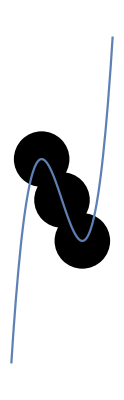

```mathematica
p=Graphics[{PointSize[0.1],{Point[{0,f[0]}],Point[{1,f[1]}],Point[{2,f[2]}]}}];
q=Plot[f[x],{x,-2,4}];
Show[p,q]
```

## Part (iii)

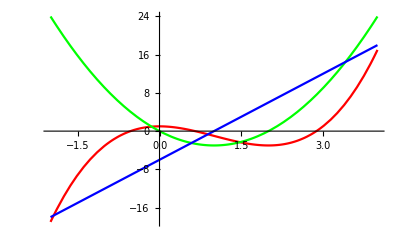

```mathematica
Plot[{f[x],f'[x],f''[x]},{x,-2,4},PlotStyle->{Red,Green,Blue}]
```

f[x] is coloured Red, f’[x] is coloured Green, f’’[x] is coloured blue

# Answer to the Question 3

## Part (a)

section (i)

```mathematica
Clear[p,q]
lhs=LogicalExpand[(p∨q)∧(p∨r)];
rhs=LogicalExpand[p∨(q∧r)];
lhs==rhs
```

True

section (ii)

```mathematica
lhs=LogicalExpand[p∧(p∨q)];
rhs=LogicalExpand[p];
lhs==rhs
```

True

section (iii)

```mathematica
lhs=LogicalExpand[p∨(p∧q)];
rhs=LogicalExpand[p];
lhs==rhs
```

True

## Part (b)

using Do loop

```mathematica
s=0;
Do[s=s+3^j/Factorial[i],{i,1,50},{j,0,i-1}]
s//N
```

8.68363

Using For loop

```mathematica
For[s=0;i=1;j=0,i≤50;j<i,i++;i++,s=s+3^j/Factorial[i]]
s//N
```

1.71828

## Part (c)

```mathematica
n=RandomInteger[{2,9999}]
```

2405

section (i)

```mathematica
d=Divisors[n]
```

{1,5,13,37,65,185,481,2405}

section (ii)

```mathematica
∑_(i=1)^Length[d] d[[i]]
```

3192

section (iii)

```mathematica
∑_(i=1)^Length[d] (d[[i]])^2
```

6055400

# Answer to the Question 4

## Part (a)

Comparing the equation with the general equation of 2nd degree

```mathematica
a=1;b=4;c=-2;
h=-5/2;g=1/2;f=1;
Det[({{a, h, g}, {h, b, f}, {g, f, c}})]
```

0

hence the equation represent a pair of straight lines

```mathematica
Print["the points of intersections are ",{(h f-b g)/(a b-h^2),(g h-a f)/(a b-h^2)}]
```

the points of intersections are {2,1}

```mathematica
Print["the angle between them is ",ArcTan[(2 Sqrt[h^2-a b])/(a+b)]//N]
```

the angle between them is 0.54042

## Part (b)

```mathematica
θ=1/2 ArcTan[(2 h)/(a-b)];
p=x^2-5 x y+4 y^2+x+2 y-2;
Expand[p/.x->X Cos[θ]-Y Sin[θ]+2/.y->X Sin[θ]+Y Cos[θ]+1]//Simplify
```

1/2 (-(-5+√34) X^2+(5+√34) Y^2)

# Answer to the Question 5

## Part (a)

```mathematica
f1=Sqrt[4 x];
f2=Sqrt[8 x-x^2];
Print["Points of intersections are ",Solve[f1==f2]]
```

Points of intersections are {{x→0},{x→4}}

```mathematica
Print["Area is ",Abs[NIntegrate[f1-f2,{x,0,4}]]," square units"]
```

Area is 1.8997 square units

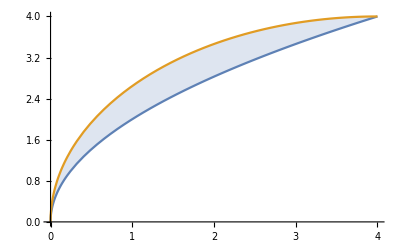

```mathematica
Plot[{f1,f2},{x,0,4},Filling->{1->{2}}]
```

## Part (b)

```mathematica
∫_-5^5 ∫_(-Sqrt[25-x^2])^Sqrt[25-x^2] ∫_(-Sqrt[25-x^2-y^2])^Sqrt[25-x^2-y^2] 1ⅆxⅆyⅆz
```

10 π (-25+x^2)

# Answer to the Question 6

## Part (a)

```mathematica
Print["Let the integers be p=",p=RandomInteger[{10000,99999}]," and q=",q=RandomInteger[{100000,999999}]]
Print["GCD is ",gcd=GCD[p,q]," and LCM is ",lcm=LCM[p,q]]
Print["Product of GCD and LCM is ",gcd*lcm]
Print["Product of the Numbers is ",p*q]
gcd*lcm==p*q
```

Let the integers be p=31447 and q=966533

GCD is 1 and LCM is 30394563251

Product of GCD and LCM is 30394563251

Product of the Numbers is 30394563251

True

## Part (b)

```mathematica
For[set={};i=1,i≤1500,i++,If[PrimeQ[i],set=AppendTo[set,i]]]
set=Append[set, ];
Do[Print[set[[i]],", ",set[[i+1]],", ",set[[i+2]],", ",set[[i+3]],", ",set[[i+4]],", ",set[[i+5]],", ",set[[i+6]],", ",set[[i+7]],", ",set[[i+8]],", ",set[[i+9]],", "],{i,1,Length[set]-1,10}]
```

2, 3, 5, 7, 11, 13, 17, 19, 23, 29,

31, 37, 41, 43, 47, 53, 59, 61, 67, 71,

73, 79, 83, 89, 97, 101, 103, 107, 109, 113,

127, 131, 137, 139, 149, 151, 157, 163, 167, 173,

179, 181, 191, 193, 197, 199, 211, 223, 227, 229,

233, 239, 241, 251, 257, 263, 269, 271, 277, 281,

283, 293, 307, 311, 313, 317, 331, 337, 347, 349,

353, 359, 367, 373, 379, 383, 389, 397, 401, 409,

419, 421, 431, 433, 439, 443, 449, 457, 461, 463,

467, 479, 487, 491, 499, 503, 509, 521, 523, 541,

547, 557, 563, 569, 571, 577, 587, 593, 599, 601,

607, 613, 617, 619, 631, 641, 643, 647, 653, 659,

661, 673, 677, 683, 691, 701, 709, 719, 727, 733,

739, 743, 751, 757, 761, 769, 773, 787, 797, 809,

811, 821, 823, 827, 829, 839, 853, 857, 859, 863,

877, 881, 883, 887, 907, 911, 919, 929, 937, 941,

947, 953, 967, 971, 977, 983, 991, 997, 1009, 1013,

1019, 1021, 1031, 1033, 1039, 1049, 1051, 1061, 1063, 1069,

1087, 1091, 1093, 1097, 1103, 1109, 1117, 1123, 1129, 1151,

1153, 1163, 1171, 1181, 1187, 1193, 1201, 1213, 1217, 1223,

1229, 1231, 1237, 1249, 1259, 1277, 1279, 1283, 1289, 1291,

1297, 1301, 1303, 1307, 1319, 1321, 1327, 1361, 1367, 1373,

1381, 1399, 1409, 1423, 1427, 1429, 1433, 1439, 1447, 1451,

1453, 1459, 1471, 1481, 1483, 1487, 1489, 1493, 1499, Null,

## Part (c)

using Do loop

```mathematica
i=1;
fact=1;
Do[fact=fact*i,{i,50}]
Print["Factorial of 50 is ",fact]
```

Factorial of 50 is 30414093201713378043612608166064768844377641568960512000000000000

Using For loop

```mathematica
For[fact=1;i=1,i≤50,i++,fact=fact*i]
Print["Factorial of 50 is ",fact]
```

Factorial of 50 is 30414093201713378043612608166064768844377641568960512000000000000

Using While loop

```mathematica
fact=1;
i=1;
While[i≤50,fact=fact*i;i++]
Print["Factorial of 50 is ",fact]
```

Factorial of 50 is 30414093201713378043612608166064768844377641568960512000000000000